```mathematica
Laplace:
```

```mathematica
ClearAll[α,σ,μ,x]
```

```mathematica
p = 1/(2σ)Exp[-Abs[x-μ]/σ]
```

ⅇ^(-Abs[x-μ]/σ)/(2 σ)

```mathematica
θ = σ;
```

```mathematica
ss = FullSimplify[D[Log[p],θ]]
```

(-σ+Abs[x-μ])/σ^2

```mathematica
ss' = FullSimplify[D[ss,θ]]
```

(σ-2 Abs[x-μ])/σ^3

```mathematica
csIntCitatel1 = FullSimplify[p^(1+α)*ss]
```

(2^(-1-α) (ⅇ^(-Abs[x-μ]/σ)/σ)^(1+α) (-σ+Abs[x-μ]))/σ^2

```mathematica
csIntCitatel2 = FullSimplify[csIntCitatel1/.(x-μ)-> y*σ,σ≥0]
```

(2^(-1-α) (ⅇ^Abs[y] σ)^(-1-α) (-1+Abs[y]))/σ

```mathematica
csIntCitatel3 = FullSimplify[Integrate[2*csIntCitatel2*σ,{y,0,∞}]]
```

ConditionalExpression[-(2^-α α σ^(-1-α))/(1+α)^2,Re[α]>-1]

```mathematica
csIntJmenovatel1 = FullSimplify[p^(1+α)]
```

2^(-1-α) (ⅇ^(-Abs[x-μ]/σ)/σ)^(1+α)

```mathematica
csIntJmenovatel2 = FullSimplify[csIntJmenovatel1/.(x-μ)-> y*σ,σ≥0]
```

2^(-1-α) (ⅇ^Abs[y] σ)^(-1-α)

```mathematica
csIntJmenovatel3 = FullSimplify[Integrate[2*csIntJmenovatel2*σ,{y,0,∞}]]
```

ConditionalExpression[(2^-α σ^-α)/(1+α),Re[α]>-1]

```mathematica
cs = FullSimplify[csIntCitatel3/csIntJmenovatel3]
```

ConditionalExpression[-α/(σ+α σ),Re[α]>-1]

```mathematica
cs' = FullSimplify[D[cs,θ]]
```

ConditionalExpression[α/((1+α) σ^2),Re[α]>-1]

```mathematica
Ia =FullSimplify[ (ss' - cs'-α(ss-cs)(cs-ss))*p^(1+α)]
```

ConditionalExpression[1/((1+α)^2 σ^4)2^(-1-α) (ⅇ^(-Abs[x-μ]/σ)/σ)^(1+α) ((1+2 α) σ^2+(1+α) Abs[x-μ] (-2 (σ+2 α σ)+α (1+α) Abs[x-μ])),Re[α]>-1]

```mathematica
Ia1 = FullSimplify[Ia/.(x-μ)->y*σ,σ≥0]
```

ConditionalExpression[1/(1+α)^2 2^(-1-α) ⅇ^(-(1+α) Abs[y]) σ^(-3-α) (1+2 α-2 (1+α) (1+2 α) Abs[y]+y α (1+α)^2 Conjugate[y]),Re[α]>-1]

```mathematica
Ia2 = FullSimplify[Integrate[2*Ia1*σ,{y,0,∞}]]
```

ConditionalExpression[-(2^-α σ^(-2-α))/(1+α)^3,Re[α]>-1]

```mathematica
IF = FullSimplify[-Ia2^(-1) * (p^α)*(ss-cs)]
```

ConditionalExpression[(1+α)^2 (ⅇ^(-Abs[x-μ]/σ)/σ)^α σ^α (-σ+(1+α) Abs[x-μ]),Re[α]>-1]

```mathematica
IF1 = FullSimplify[IF/.μ->0]
```

ConditionalExpression[(1+α)^2 (ⅇ^(-Abs[x]/σ)/σ)^α σ^α (-σ+(1+α) Abs[x]),Re[α]>-1]

```mathematica
IFun = Function[{σ,α} ,(1+α)^2 (ⅇ^(-Abs[x]/σ)/σ)^α σ^α (-σ+(1+α) Abs[x])];
```

```mathematica
Needs["PlotLegends`"]
```

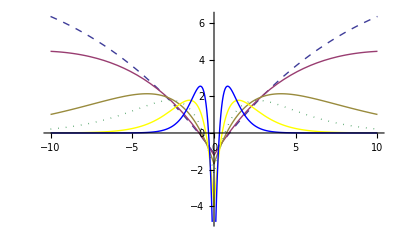

```mathematica
Plot[{
IFun[1,0.05],
IFun[1,0.1],
IFun[1,0.3],
IFun[1,0.5],
IFun[1,1],
IFun[1,2]},
{x,-10,10},
PlotLegend->{"α = 0.05","α = 0.1","α = 0.3","α = 0.5","α = 1","α = 2"},
LegendPosition->{1,-0.4},
PlotStyle->{Dashed, Thick,Thin, Dotted, Yellow, Blue}
]
```

```mathematica
Normalni:
```

```mathematica
ClearAll[α,σ,μ,x]
```

```mathematica
θ = μ
```

μ

```mathematica
ss = FullSimplify[D[Log[p],θ]]
```

Abs'[x-μ]/σ

```mathematica
ss' = FullSimplify[D[ss,θ]]
```

-Abs''[x-μ]/σ

```mathematica
csIntCitatel1 = FullSimplify[p^(1+α)*ss]
```

(2^(-1-α) (ⅇ^(-Abs[x-μ]/σ)/σ)^(1+α) Abs'[x-μ])/σ

```mathematica
csIntCitatel2 = FullSimplify[csIntCitatel1/.(x-μ)-> y*σ,{σ≥0,y≥0}]
```

2^(-1-α) ⅇ^(-y (1+α)) σ^(-2-α) Sign[y] Sign[σ]

```mathematica
csIntCitatel3 = FullSimplify[Integrate[2*csIntCitatel2*σ,{y,0,∞}]]
```

ConditionalExpression[(2^-α σ^(-1-α) Sign[σ])/(1+α),Re[α]>-1]

```mathematica
csIntJmenovatel1 = FullSimplify[p^(1+α)]
```

2^(-1-α) (ⅇ^(-Abs[x-μ]/σ)/σ)^(1+α)

```mathematica
csIntJmenovatel2 = FullSimplify[csIntJmenovatel1/.(x-μ)-> y*σ,{σ≥0,y≥0}]
```

2^(-1-α) (ⅇ^y σ)^(-1-α)

```mathematica
csIntJmenovatel3 = FullSimplify[Integrate[csIntJmenovatel2*σ*2,{y,0,∞}]]
```

ConditionalExpression[(2^-α σ^-α)/(1+α),Re[α]>-1]

```mathematica
cs = FullSimplify[csIntCitatel3/csIntJmenovatel3]
```

ConditionalExpression[Sign[σ]/σ,Re[α]>-1]

```mathematica
cs' = FullSimplify[D[cs,θ]]
```

0

```mathematica
Ia =FullSimplify[ (ss' - cs'-α(ss-cs)(cs-ss))*p^(1+α)]
```

ConditionalExpression[(2^(-1-α) (ⅇ^((-x+μ)/(σ Sign[x-μ]))/σ)^(1+α) (α (Sign[σ]-Abs'[x-μ])^2-σ Abs''[x-μ]))/σ^2,Re[α]>-1]

```mathematica
Ia1 = FullSimplify[Ia/.(x-μ)->y*σ,{σ≥0}]
```

ConditionalExpression[(2^(-1-α) (ⅇ^((-x+μ)/(σ Sign[y]))/σ)^(1+α) (α (Sign[σ]-Abs'[y σ])^2-σ Abs''[y σ]))/σ^2,Re[α]>-1]

```mathematica
Ia2 = FullSimplify[Ia1/.(-x+μ)->-y*σ,{σ>0,y>0}]
```

ConditionalExpression[-2^(-1-α) ⅇ^y (ⅇ^y σ)^(-2-α) Abs''[y σ],Re[α]>-1]

```mathematica
Ia2 = FullSimplify[Integrate[Ia1*σ*2,{y,0,∞}]]
```

Integrate::idiv: Integral of α (Sign[σ] - SuperscriptBox[ does not converge on {0, ∞}.

∫_0^∞ ConditionalExpression[(2^-α (ⅇ^((-x+μ)/(σ Sign[y]))/σ)^(1+α) (α (Sign[σ]-Abs'[y σ])^2-σ Abs''[y σ]))/σ,Re[α]>-1]ⅆy

```mathematica
IF = FullSimplify[-Ia2^(-1) * (p^α)*(ss-cs)]
```

ConditionalExpression[(1+α)^(3/2) (x-μ) σ (σ^2)^(1/2 (-1+α)) ((ⅇ^(-(x-μ)^2/(2 σ^2)))/(√(σ^2)))^α,Re[α]>-1]

```mathematica
IF1 = FullSimplify[IF/.σ->1]
```

ConditionalExpression[(ⅇ^(-1/2 (x-μ)^2))^α (1+α)^(3/2) (x-μ),Re[α]>-1]

```mathematica
IFun = Function[{μ,α} ,(ⅇ^(-1/2 (x-μ)^2))^α (1+α)^(3/2) (x-μ)];
```

```mathematica
Needs["PlotLegends`"]
```

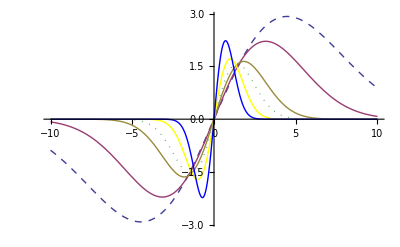

```mathematica
Plot[{
IFun[0,0.05],
IFun[0,0.1],
IFun[0,0.3],
IFun[0,0.5],
IFun[0,1],
IFun[0,2]},
{x,-10,10},
PlotLegend->{"α = 0.05","α = 0.1","α = 0.3","α = 0.5","α = 1","α = 2"},
LegendPosition->{1,-0.4},
PlotStyle->{Dashed, Thick,Thin, Dotted, Yellow, Blue}
]
```